## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"]
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

## 设置non-GR参数字符flag Gw@150914!

```mathematica
eventID="GW170729";

deviationType="cpsi";
deviationOrders=List[0,2,3,4,"5l",6,"6l"];
deviationNames=List["cpsi0","cpsi2","cpsi3","cpsi4","cpsi5l","cpsi6","cpsi6l"];
psiNames=List["psi0","psi2","psi3","psi4","psi5l","psi6","psi6l"];

deviationOrders=List[0,2,4,6,"6l",7];
deviationNames=List["cpsi0","cpsi2","cpsi4","cpsi6","cpsi6l","cpsi7"];
psiNames=List["psi0","psi2","psi4","psi6","psi6l","cpsi7"];
```

```mathematica
"alpha3"
```

alpha3

```mathematica
"3, 4, 5l, 6; 0, 2, 6l"
```

3, 4, 5l, 6; 0, 2, 6l

```mathematica
csvPath="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv"<>"\\"<>eventID;
csvNames=eventID<>"_"<>#<>".csv"& /@ deviationNames;

csvFilePaths=csvPath<>"\\"<>#& /@ csvNames;
```

### from CSV

```mathematica
samples=<||>;
Do[
CSVSamples=Import["D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv\\"<>eventID<>"\\"<>eventID<>"_"<>n<>".csv"];
samples[n]=<||>;
samples[n]["mass1"]=CSVSamples[[All,1]][[2;;]];
samples[n]["mass2"]=CSVSamples[[All,2]][[2;;]];
samples[n]["spin1z"]=CSVSamples[[All,3]][[2;;]];
samples[n]["spin2z"]=CSVSamples[[All,4]][[2;;]];
samples[n]["eta"]=CSVSamples[[All,5]][[2;;]];
samples[n]["Mchirp"]=CSVSamples[[All,6]][[2;;]];
samples[n][n]=CSVSamples[[All,7]][[2;;]];
samples[n]["chis"]=χs[samples["spin1z"],samples["spin2z"]];
samples[n]["chia"]=χa[samples["spin1z"],samples["spin2z"]];,
{n,deviationNames}
]
```

### Calculate GR Coefficients

```mathematica
Do[
samples[deviationNames[[n]]][psiNames[[n]]]=MapThread[
Psi[deviationOrders[[n]],η[#1,#2],M[#1,#2],#3,#4]&,
{samples[deviationNames[[n]]]["mass1"],samples[deviationNames[[n]]]["mass2"],samples[deviationNames[[n]]]["spin1z"],samples[deviationNames[[n]]]["spin2z"]}
];,
{n,Range[Length[deviationOrders]]}
]
```

### Calculate BCIs

```mathematica
BCI=<||>;
Do[
BCI[deviationNames[[n]]]=<||>;
BCI[deviationNames[[n]]]["mass1"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["mass1"],Subscript["m","1"]][[1]];
BCI[deviationNames[[n]]]["mass2"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["mass2"],Subscript["m","2"]][[1]];
BCI[deviationNames[[n]]]["spin1z"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["spin1z"],"spin1z"][[1]];
BCI[deviationNames[[n]]]["spin2z"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["spin2z"],"spin2z"][[1]];
BCI[deviationNames[[n]]][deviationNames[[n]]]=PlotParameterWithBCI[samples[deviationNames[[n]]][deviationNames[[n]]],deviationNames[[n]]][[1]];
BCI[deviationNames[[n]]][psiNames[[n]]]=PlotParameterWithBCI[samples[deviationNames[[n]]][psiNames[[n]]],psiNames[[n]]][[1]];,
{n,Range[Length[deviationOrders]]}
]
```

```mathematica
widths={};
Do[
AppendTo[widths,(BCI[deviationNames[[n]]][deviationNames[[n]]][[3]]-BCI[deviationNames[[n]]][deviationNames[[n]]][[1]])/(BCI[deviationNames[[n]]][psiNames[[n]]][[3]]-BCI[deviationNames[[n]]][psiNames[[n]]][[1]])],
{n,Range[Length[deviationOrders]]}
];
Round[widths,0.0001]
widths={};
Do[
AppendTo[widths,BCI[deviationNames[[n]]][deviationNames[[n]]][[3]]-BCI[deviationNames[[n]]][deviationNames[[n]]][[1]]],
{n,Range[Length[deviationOrders]]}
];
Round[widths/{5000,250,150,5,1.5,0.5,0.1},0.0001]
```

{0.4127,1.9662,13.1357,19.4828,19.8434,1.}

Thread::tdlen: Objects of unequal length in {1657.45,399.578,206.177,194.283,12.6996,3.37566} {1/5000,1/250,1/150,1/5,0.666667,2.,10.} cannot be combined.

Round[{1657.45,399.578,206.177,194.283,12.6996,3.37566} {1/5000,1/250,1/150,1/5,0.666667,2.,10.},0.0001]

```mathematica
medians={};
Do[
AppendTo[medians,BCI[deviationNames[[n]]][deviationNames[[n]]][[2]]/BCI[deviationNames[[n]]][psiNames[[n]]][[2]]],
{n,Range[Length[deviationOrders]]}
];
Round[medians,0.0001]
```

{0.5455,1.6503,9.1711,-19.0963,10.2107,1.}

## m1-m2 Plot, 22

```mathematica
pInterval=<||>;
tapeIntervals=<||>;
tapes=<||>;
plots=<||>;
compPlots=<||>;
lines=<||>;
legends=<||>;

m1m2=<||>;
m1PriorRange=<||>;
m2PriorRange=<||>;
m1m2PDF=<||>;
contourPD=<||>;
contourPlotObj=<||>;
contourPoints=<||>;
smoothedContourPoints=<||>;
```

```mathematica
(*==========================================================*)
```

===== 第i$199457条等高线 =====

包含闭合区域数：1

区域内总积分值：0.882512

可信水平百分比：88.2512%

==========================

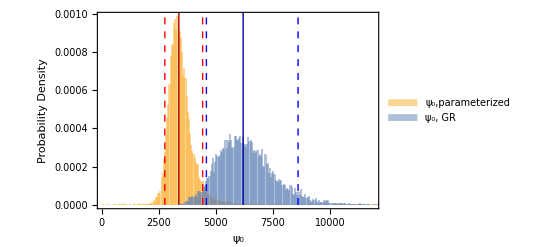

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

原始数据量 = 43305，降采样后数据量 = 43305（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在先验区间内的积分值 = 0.999946（未归一化，无需=1）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.000408}

等高线数量：1 条

第一条等高线的前5个边界点：{{53.7315,19.1728},{51.5421,19.888},{51.7341,20.4493},{47.5964,22.1213},{42.8834,23.8456}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$201841条等高线 =====

包含闭合区域数：1

区域内总积分值：0.883151

可信水平百分比：88.3151%

==========================

已绘制等高线值：{0.0009}

等高线数量：1 条

第一条等高线的前5个边界点：{{47.5376,26.0624},{48.5448,25.3033},{47.0605,23.8456},{49.9587,22.7853},{53.7315,21.2607}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$188614条等高线 =====

包含闭合区域数：1

区域内总积分值：0.720912

可信水平百分比：72.0912%

==========================

```mathematica
order=0;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.000408};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

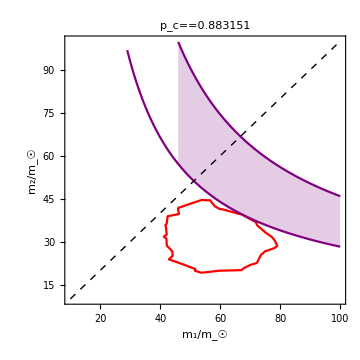

```mathematica
m1s=Range[10,100,1];
m2s=Range[10,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

(*tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];*)

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

(*tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};*)

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Select[tapes[n][n][[1]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],
Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,0]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{3->{2}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

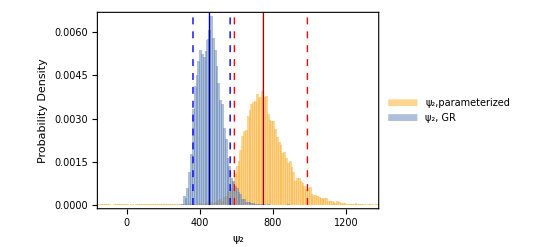

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

原始数据量 = 47527，降采样后数据量 = 47527（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在先验区间内的积分值 = 1.（未归一化，无需=1）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.00041}

等高线数量：1 条

第一条等高线的前5个边界点：{{49.8936,41.6547},{53.7315,42.4777},{56.0556,42.9803},{60.7722,43.5688},{60.8585,43.6092}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$205606条等高线 =====

包含闭合区域数：1

区域内总积分值：0.863942

可信水平百分比：86.3942%

==========================

```mathematica
order=2;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.00041};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

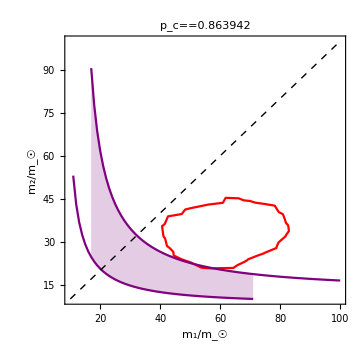

```mathematica
m1s=Range[10,100,1];
m2s=Range[10,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

(*tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];*)

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

(*tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};*)

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Select[tapes[n][n][[1]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],
Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,0]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{3->{2}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

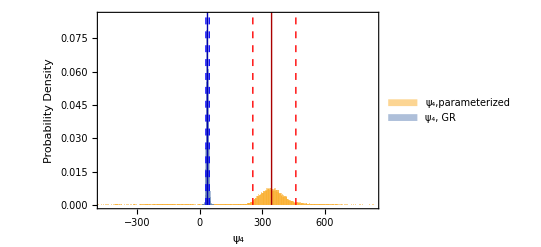

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

原始数据量 = 50837，降采样后数据量 = 50837（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在先验区间内的积分值 = 1.（未归一化，无需=1）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.001}

等高线数量：1 条

第一条等高线的前5个边界点：{{53.7315,26.0438},{52.9488,27.5832},{52.9073,27.8031},{52.8166,28.0603},{53.689,31.7488}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$215262条等高线 =====

包含闭合区域数：1

区域内总积分值：0.553985

可信水平百分比：55.3985%

==========================

```mathematica
order=4;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

```mathematica
m1s=Range[10,100,1];
m2s=Range[10,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

(*tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];*)

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

(*tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};*)

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Select[tapes[n][n][[1]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],
Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,0]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{3->{2}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

ListLinePlot::lpn: {{{53.7315,26.0438},{52.9488,27.5832},{52.9073,27.8031},{52.8166,28.0603},{53.689,31.7488},{53.6709,31.7607},{53.6814,31.7748},{53.7315,31.7958},{56.0074,33.7395},{57.1341,34.762},«31»},{},{}} is not a list of numbers or pairs of numbers.

ListLinePlot[{{{53.7315,26.0438},{52.9488,27.5832},{52.9073,27.8031},{52.8166,28.0603},{53.689,31.7488},{53.6709,31.7607},{53.6814,31.7748},{53.7315,31.7958},{56.0074,33.7395},{57.1341,34.762},{58.42,35.7183},{59.7138,37.3996},{60.1335,37.8766},{59.9959,39.6759},{60.7722,40.5175},{65.3622,40.3647},{67.8129,40.2421},{68.7001,39.9252},{69.2773,39.6759},{74.8537,38.0235},{75.3663,37.8412},{75.5829,37.4922},{75.5804,35.7183},{75.4865,33.9174},{75.7443,33.4892},{77.6905,31.7607},{79.3309,31.0403},{80.3156,28.2469},{80.1919,27.8031},{80.0003,27.2708},{78.8813,24.6924},{74.8537,23.8735},{74.7571,23.8456},{71.7079,22.7509},{67.8129,22.225},{60.8041,21.8758},{60.7722,21.8752},{56.0818,23.8456},{55.1507,24.2445},{53.8243,25.8244},{53.7315,26.0438}},{},{}},PlotStyle→{RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],RGBColor[0.5, 0, 0.5]},Filling→{3→{2}},Axes→False,Frame→True,FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},FrameLabel→{m_1/m_☉,m_2/m_☉},FrameStyle→Directive[GrayLevel[0],Thickness[0.004]],BaseStyle→{FontSize→15},AspectRatio→1,PlotRange→{{10,100},{10,100}},Epilog→{Inset[,Scaled[{0.2,0.82}],{0,0}],GrayLevel[0],Dashing[{Small,Small}],Line[{{0,0},{100,100}}]},PlotLabel→p_c==0.553985,ImageSize→Medium]

## (Deprecated) m1-m2 Plot, 22

-Graphics-

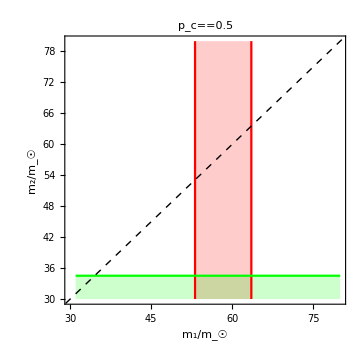

```mathematica
m1s=Range[30,80,1];
m2s=Range[30,80,1];

order=0;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.0;
prob=0.5;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
(*Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]*)};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,2]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

-Graphics-

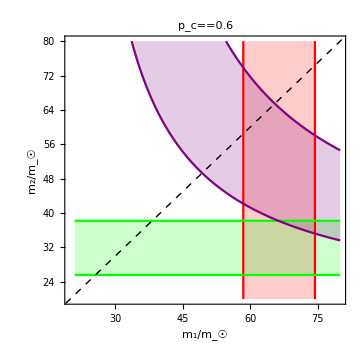

```mathematica
m1s=Range[20,80,1];
m2s=Range[20,80,1];

order=4;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.0;
prob=0.6;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
(*Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]*)};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,2]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.902^3
```

0.266129

HistogramList::ldata: Missing[KeyAbsent,cpsi3][cpsi3] is not a valid dataset or list of datasets.

HistogramList::ldata: Missing[KeyAbsent,cpsi3][psi3] is not a valid dataset or list of datasets.

Part::partw: Part 3 of Quantile[Missing[KeyAbsent,cpsi3][cpsi3],{0.05,0.5,0.95}] does not exist.

Part::partw: Part 3 of Quantile[Missing[KeyAbsent,cpsi3][psi3],{0.05,0.5,0.95}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

0.3997 ； Null

Part::partw: Part 2 of {(1.841158402001887 (20.5+h)^(4/3) (-50.2655+0.1666666666666667 (-1558. h Power[«2»] Plus[«2»]+113. Plus[«4»])))/h==Missing[KeyAbsent,cpsi3][cpsi3]} does not exist.

Part::partw: Part 2 of {(1.797321297192318 (21.+h)^(4/3) (-50.2655+0.1666666666666667 (-1596. h Power[«2»] Plus[«2»]+113. Plus[«4»])))/h==Missing[KeyAbsent,cpsi3][cpsi3]} does not exist.

Part::partw: Part 2 of {(1.755523127490171 (21.5+h)^(4/3) (-50.2655+0.1666666666666667 (-1634. h Power[«2»] Plus[«2»]+113. Plus[«4»])))/h==Missing[KeyAbsent,cpsi3][cpsi3]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

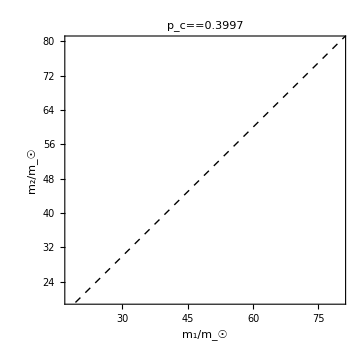

```mathematica
m1s=Range[20,80,1/2];
m2s=Range[20,80,1/2];

order=3;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.0;
prob=0.342;
prob=0.3997；

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{3,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,3]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{18,m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],
Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.495^3
```

0.878713

```mathematica
tapes[n][n]
```

{{{20,-963.289-2.18834×10^-12 ⅈ},{41/2,-963.289-2.18834×10^-12 ⅈ},{21,-963.289-2.18834×10^-12 ⅈ},{43/2,-963.289-2.18834×10^-12 ⅈ},{22,-963.289-2.18834×10^-12 ⅈ},{45/2,-963.289-2.18834×10^-12 ⅈ},{23,-963.289-2.18834×10^-12 ⅈ},{47/2,-963.289-2.18834×10^-12 ⅈ},{24,-963.289-2.18834×10^-12 ⅈ},{49/2,-963.289-2.18834×10^-12 ⅈ},{25,-963.289-2.18834×10^-12 ⅈ},{51/2,-963.289+8.35545×10^-13 ⅈ},{26,-963.289-2.26743×10^-12 ⅈ},{53/2,-963.289-2.26743×10^-12 ⅈ},{27,-963.289-2.26743×10^-12 ⅈ},{55/2,-963.289-5.96162×10^-13 ⅈ},{28,-963.289+1.11538×10^-12 ⅈ},{57/2,-963.289+1.11538×10^-12 ⅈ},{29,-963.289-6.77171×10^-13 ⅈ},{59/2,-963.289+1.1561×10^-12 ⅈ},{30,-963.289+1.1561×10^-12 ⅈ},{61/2,-963.289+1.1561×10^-12 ⅈ},{31,-963.289+1.1561×10^-12 ⅈ},{63/2,-963.289+1.1561×10^-12 ⅈ},{32,-963.289+1.1561×10^-12 ⅈ},{65/2,-963.289+1.1561×10^-12 ⅈ},{33,-963.289+1.1561×10^-12 ⅈ},{67/2,-963.289+1.1561×10^-12 ⅈ},{34,-963.289+1.1561×10^-12 ⅈ},{69/2,-963.289+1.1561×10^-12 ⅈ},{35,-963.289+1.1561×10^-12 ⅈ},{71/2,-963.289-1.17415×10^-12 ⅈ},{36,-963.289+1.19804×10^-12 ⅈ},{73/2,-963.289-1.21615×10^-12 ⅈ},{37,-963.289+1.2401×10^-12 ⅈ},{75/2,-963.289-1.25826×10^-12 ⅈ},{38,-963.289+1.28226×10^-12 ⅈ},{77/2,-963.289-1.30046×10^-12 ⅈ},{39,-963.289+1.3245×10^-12 ⅈ},{79/2,-963.289-1.34275×10^-12 ⅈ},{40,-963.289+1.36682×10^-12 ⅈ},{81/2,-963.289-1.3851×10^-12 ⅈ},{41,-963.289-1.3851×10^-12 ⅈ},{83/2,-963.289+1.45163×10^-12 ⅈ},{42,-963.289-1.42754×10^-12 ⅈ},{85/2,-963.289+1.49409×10^-12 ⅈ},{43,-963.289-1.47003×10^-12 ⅈ},{87/2,-963.289+1.5366×10^-12 ⅈ},{44,-963.289-1.51256×10^-12 ⅈ},{89/2,-963.289+1.57915×10^-12 ⅈ},{45,-963.289+1.57915×10^-12 ⅈ},{91/2,-963.289-1.59769×10^-12 ⅈ},{46,-963.289-1.59769×10^-12 ⅈ},{93/2,-963.289+3.33158×10^-14 ⅈ},{47,-963.289-1.61899×10^-12 ⅈ},{95/2,-963.289-1.61899×10^-12 ⅈ},{48,-963.289-1.61899×10^-12 ⅈ},{97/2,-963.289-1.61899×10^-12 ⅈ},{49,-963.289-1.61899×10^-12 ⅈ},{99/2,-963.289-1.61899×10^-12 ⅈ},{50,-963.289-1.61899×10^-12 ⅈ},{101/2,-963.289-1.61899×10^-12 ⅈ},{51,-963.289-1.61899×10^-12 ⅈ},{103/2,-963.289-1.61899×10^-12 ⅈ},{52,-963.289-1.61899×10^-12 ⅈ},{105/2,-963.289-1.61899×10^-12 ⅈ},{53,-963.289-1.61899×10^-12 ⅈ},{107/2,-963.289-1.61899×10^-12 ⅈ},{54,-963.289-1.61899×10^-12 ⅈ},{109/2,-963.289+3.52948×10^-13 ⅈ},{55,-963.289-1.64029×10^-12 ⅈ},{111/2,-963.289+3.7424×10^-13 ⅈ},{56,-963.289-1.66158×10^-12 ⅈ},{113/2,-963.289-1.66158×10^-12 ⅈ},{57,-963.289-1.66158×10^-12 ⅈ},{115/2,-963.289-1.66158×10^-12 ⅈ},{58,-963.289+4.59342×10^-13 ⅈ},{117/2,-963.289-1.68284×10^-12 ⅈ},{59,-963.289-1.68284×10^-12 ⅈ},{119/2,-963.289-1.68284×10^-12 ⅈ},{60,-963.289+5.23098×10^-13 ⅈ},{121/2,-963.289-1.70408×10^-12 ⅈ},{61,-963.289-1.70408×10^-12 ⅈ},{123/2,-963.289-1.70408×10^-12 ⅈ},{62,-963.289-1.70408×10^-12 ⅈ},{125/2,-963.289-1.70408×10^-12 ⅈ},{63,-963.289-1.70408×10^-12 ⅈ},{127/2,-963.289-1.70408×10^-12 ⅈ},{64,-963.289-1.70408×10^-12 ⅈ},{129/2,-963.289-1.70408×10^-12 ⅈ},{65,-963.289-1.70408×10^-12 ⅈ},{131/2,-963.289-1.70408×10^-12 ⅈ},{66,-963.289-1.70408×10^-12 ⅈ},{133/2,-963.289-1.70408×10^-12 ⅈ},{67,-963.289-1.70408×10^-12 ⅈ},{135/2,-963.289-1.70408×10^-12 ⅈ},{68,-963.289+8.40904×10^-13 ⅈ},{137/2,-963.289-1.72521×10^-12 ⅈ},{69,-963.289-1.72521×10^-12 ⅈ},{139/2,-963.289+8.83145×10^-13 ⅈ},{70,-963.289-1.74632×10^-12 ⅈ},{141/2,-963.289-1.74632×10^-12 ⅈ},{71,-963.289-1.74632×10^-12 ⅈ},{143/2,-963.289-1.74632×10^-12 ⅈ},{72,-963.289-1.74632×10^-12 ⅈ},{145/2,-963.289+9.88592×10^-13 ⅈ},{73,-963.289-1.76739×10^-12 ⅈ},{147/2,-963.289+1.00965×10^-12 ⅈ},{74,-963.289-1.78844×10^-12 ⅈ},{149/2,-963.289-1.78844×10^-12 ⅈ},{75,-963.289+1.05175×10^-12 ⅈ},{151/2,-963.289-1.80948×10^-12 ⅈ},{76,-963.289+1.06585×10^-12 ⅈ},{153/2,-963.289-1.81692×10^-12 ⅈ},{77,-963.289-1.81692×10^-12 ⅈ},{155/2,-963.289+1.0804×10^-12 ⅈ},{78,-963.289+1.0804×10^-12 ⅈ},{157/2,-963.289-1.83106×10^-12 ⅈ},{79,-963.289-1.83106×10^-12 ⅈ},{159/2,-963.289+1.09415×10^-12 ⅈ},{80,-963.289-1.83779×10^-12 ⅈ},{161/2,-963.289+1.10079×10^-12 ⅈ},{81,-963.289-1.84434×10^-12 ⅈ},{163/2,-963.289+1.10725×10^-12 ⅈ},{82,-963.289-1.8507×10^-12 ⅈ},{165/2,-963.289+1.11352×10^-12 ⅈ},{83,-963.289+1.11352×10^-12 ⅈ},{167/2,-963.289-1.863×10^-12 ⅈ},{84,-963.289+1.11955×10^-12 ⅈ},{169/2,-963.289-1.86895×10^-12 ⅈ},{85,-963.289+1.12541×10^-12 ⅈ},{171/2,-963.289-1.87473×10^-12 ⅈ},{86,-963.289-1.87473×10^-12 ⅈ},{173/2,-963.289-1.87473×10^-12 ⅈ},{87,-963.289+1.14231×10^-12 ⅈ},{175/2,-963.289-1.88021×10^-12 ⅈ},{88,-963.289-1.88021×10^-12 ⅈ},{177/2,-963.289-1.88021×10^-12 ⅈ},{89,-963.289-1.88021×10^-12 ⅈ},{179/2,-963.289+1.16353×10^-12 ⅈ},{90,-963.289-3.6091×10^-13 ⅈ},{181/2,-963.289+1.16606×10^-12 ⅈ},{91,-963.289+1.16606×10^-12 ⅈ},{183/2,-963.289+1.16606×10^-12 ⅈ},{92,-963.289-3.68314×10^-13 ⅈ},{185/2,-963.289+1.16846×10^-12 ⅈ},{93,-963.289-3.70688×10^-13 ⅈ},{187/2,-963.289+1.17081×10^-12 ⅈ},{94,-963.289+1.17081×10^-12 ⅈ},{189/2,-963.289-3.75288×10^-13 ⅈ},{95,-963.289+1.17306×10^-12 ⅈ},{191/2,-963.289+1.17306×10^-12 ⅈ},{96,-963.289-3.79716×10^-13 ⅈ},{193/2,-963.289+1.17524×10^-12 ⅈ},{97,-963.289+1.17524×10^-12 ⅈ},{195/2,-963.289+1.17524×10^-12 ⅈ},{98,-963.289-3.86075×10^-13 ⅈ},{197/2,-963.289+1.17731×10^-12 ⅈ},{99,-963.289+1.17731×10^-12 ⅈ},{199/2,-963.289-3.90135×10^-13 ⅈ},{100,-963.289+1.1793×10^-12 ⅈ}},{{20,0.283622},{41/2,0.288154},{21,0.292648},{43/2,0.297106},{22,0.301528},{45/2,0.305916},{23,0.31027},{47/2,0.314592},{24,0.318883},{49/2,0.323142},{25,0.327373},{51/2,0.331574},{26,0.335747},{53/2,0.339892},{27,0.344011},{55/2,0.348103},{28,0.352171},{57/2,0.356213},{29,0.360231},{59/2,0.364225},{30,0.368196},{61/2,0.372145},{31,0.376071},{63/2,0.379976},{32,0.38386},{65/2,0.387723},{33,0.391565},{67/2,0.395388},{34,0.399191},{69/2,0.402975},{35,0.406741},{71/2,0.410488},{36,0.414217},{73/2,0.417928},{37,0.421622},{75/2,0.425299},{38,0.428959},{77/2,0.432602},{39,0.43623},{79/2,0.439841},{40,0.443437},{81/2,0.447018},{41,0.450584},{83/2,0.454134},{42,0.457671},{85/2,0.461192},{43,0.4647},{87/2,0.468194},{44,0.471674},{89/2,0.47514},{45,0.478594},{91/2,0.482034},{46,0.485461},{93/2,0.488876},{47,0.492278},{95/2,0.495667},{48,0.499045},{97/2,0.502411},{49,0.505764},{99/2,0.509106},{50,0.512437},{101/2,0.515756},{51,0.519064},{103/2,0.522361},{52,0.525647},{105/2,0.528922},{53,0.532187},{107/2,0.535441},{54,0.538685},{109/2,0.541918},{55,0.545142},{111/2,0.548355},{56,0.551559},{113/2,0.554753},{57,0.557937},{115/2,0.561112},{58,0.564277},{117/2,0.567433},{59,0.57058},{119/2,0.573718},{60,0.576846},{121/2,0.579966},{61,0.583077},{123/2,0.58618},{62,0.589274},{125/2,0.592359},{63,0.595436},{127/2,0.598504},{64,0.601565},{129/2,0.604617},{65,0.607661},{131/2,0.610698},{66,0.613726},{133/2,0.616746},{67,0.619759},{135/2,0.622764},{68,0.625762},{137/2,0.628752},{69,0.631735},{139/2,0.63471},{70,0.637678},{141/2,0.640639},{71,0.643593},{143/2,0.646539},{72,0.649479},{145/2,0.652411},{73,0.655337},{147/2,0.658256},{74,0.661168},{149/2,0.664074},{75,0.666973},{151/2,0.669865},{76,0.672751},{153/2,0.67563},{77,0.678503},{155/2,0.68137},{78,0.68423},{157/2,0.687084},{79,0.689932},{159/2,0.692773},{80,0.695609},{161/2,0.698439},{81,0.701262},{163/2,0.70408},{82,0.706892},{165/2,0.709698},{83,0.712498},{167/2,0.715293},{84,0.718082},{169/2,0.720865},{85,0.723643},{171/2,0.726415},{86,0.729181},{173/2,0.731942},{87,0.734698},{175/2,0.737448},{88,0.740193},{177/2,0.742933},{89,0.745667},{179/2,0.748396},{90,0.75112},{181/2,0.753839},{91,0.756553},{183/2,0.759261},{92,0.761965},{185/2,0.764664},{93,0.767357},{187/2,0.770046},{94,0.77273},{189/2,0.775409},{95,0.778083},{191/2,0.780753},{96,0.783418},{193/2,0.786078},{97,0.788733},{195/2,0.791383},{98,0.794029},{197/2,0.796671},{99,0.799308},{199/2,0.80194},{100,0.804568}}}

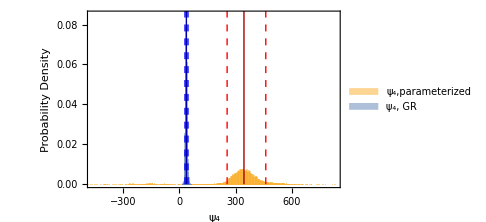

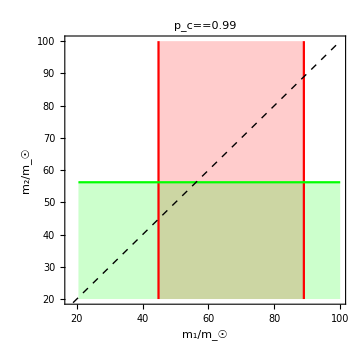

```mathematica
m1s=Range[20,100,1/2];
m2s=Range[20,100,1/2];

order=4;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.99;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{18,m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],
Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.9772^3
```

0.0668523

```mathematica
1-0.925^3
```

0.208547

HistogramList::ldata: Missing[KeyAbsent,cpsi5l][cpsi5l] is not a valid dataset or list of datasets.

HistogramList::ldata: Missing[KeyAbsent,cpsi5l][psi5l] is not a valid dataset or list of datasets.

Part::partw: Part 3 of Quantile[Missing[KeyAbsent,cpsi5l][cpsi5l],{0.05,0.5,0.95}] does not exist.

Part::partw: Part 3 of Quantile[Missing[KeyAbsent,cpsi5l][psi5l],{0.05,0.5,0.95}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

Part::partw: Part 2 of {Psi[5l,(20.33333333333333 h)/(20.33333333333333+h)^2,20.33333333333333+h,Missing[KeyAbsent,cpsi5l][spin1z]⟦2⟧,Missing[KeyAbsent,cpsi5l][spin2z]⟦2⟧]==Missing[KeyAbsent,cpsi5l][cpsi5l]} does not exist.

Part::partw: Part 2 of {Psi[5l,(20.66666666666667 h)/(20.66666666666667+h)^2,20.66666666666667+h,Missing[KeyAbsent,cpsi5l][spin1z]⟦2⟧,Missing[KeyAbsent,cpsi5l][spin2z]⟦2⟧]==Missing[KeyAbsent,cpsi5l][cpsi5l]} does not exist.

Part::partw: Part 2 of {Psi[5l,(21. h)/(21.+h)^2,21.+h,Missing[KeyAbsent,cpsi5l][spin1z]⟦2⟧,Missing[KeyAbsent,cpsi5l][spin2z]⟦2⟧]==Missing[KeyAbsent,cpsi5l][cpsi5l]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

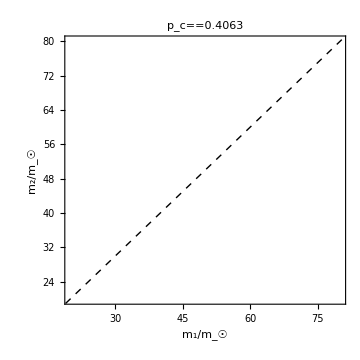

```mathematica
m1s=Range[20,80,1/3];
m2s=Range[20,80,1/3];

order="5l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.397;
prob=0.295;
prob=0.4063;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,"5l"]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
Quantile[samples[n]["cpsi5l"],pInterval[n]]
```

{-3.85518,6.61287}

```mathematica
Quantile[samples[n]["psi5l"],pInterval[n]]
```

{3.79381,7.57688}

```mathematica
tapes[n][n][[2]][[2;;]]
```

{{61/3,24.3759},{62/3,24.7755},{21,25.1751},{64/3,25.5747},{65/3,25.9744},{22,26.374},{67/3,26.7736},{68/3,27.1732},{23,27.5728},{70/3,27.9724},{71/3,28.372},{24,28.7716},{73/3,29.1712},{74/3,29.5708},{25,29.9704},{76/3,30.37},{77/3,30.7696},{26,31.1692},{79/3,31.5688},{80/3,31.9684},{27,32.368},{82/3,32.7676},{83/3,33.1673},{28,33.5669},{85/3,33.9665},{86/3,34.3661},{29,34.7657},{88/3,35.1653},{89/3,35.5649},{30,35.9645},{91/3,36.3641},{92/3,36.7637},{31,37.1633},{94/3,37.5629},{95/3,37.9625},{32,38.3621},{97/3,38.7617},{98/3,39.1613},{33,39.5609},{100/3,39.9605},{101/3,40.3602},{34,40.7598},{103/3,41.1594},{104/3,41.559},{35,41.9586},{106/3,42.3582},{107/3,42.7578},{36,43.1574},{109/3,43.557},{110/3,43.9566},{37,44.3562},{112/3,44.7558},{113/3,45.1554},{38,45.555},{115/3,45.9546},{116/3,46.3542},{39,46.7538},{118/3,47.1534},{119/3,47.553},{40,47.9527},{121/3,48.3523},{122/3,48.7519},{41,49.1515},{124/3,49.5511},{125/3,49.9507},{42,50.3503},{127/3,50.7499},{128/3,51.1495},{43,51.5491},{130/3,51.9487},{131/3,52.3483},{44,52.7479},{133/3,53.1475},{134/3,53.5471},{45,53.9467},{136/3,54.3463},{137/3,54.7459},{46,55.1456},{139/3,55.5452},{140/3,55.9448},{47,56.3444},{142/3,56.744},{143/3,57.1436},{48,57.5432},{145/3,57.9428},{146/3,58.3424},{49,58.742},{148/3,59.1416},{149/3,59.5412},{50,59.9408},{151/3,60.3404},{152/3,60.74},{51,61.1396},{154/3,61.5392},{155/3,61.9388},{52,62.3384},{157/3,62.7381},{158/3,63.1377},{53,63.5373},{160/3,63.9369},{161/3,64.3365},{54,64.7361},{163/3,65.1357},{164/3,65.5353},{55,65.9349},{166/3,66.3345},{167/3,66.7341},{56,67.1337},{169/3,67.5333},{170/3,67.9329},{57,68.3325},{172/3,68.7321},{173/3,69.1317},{58,69.5313},{175/3,69.931},{176/3,70.3306},{59,70.7302},{178/3,71.1298},{179/3,71.5294},{60,71.929},{181/3,72.3286},{182/3,72.7282},{61,73.1278},{184/3,73.5274},{185/3,73.927},{62,74.3266},{187/3,74.7262},{188/3,75.1258},{63,75.5254},{190/3,75.925},{191/3,76.3246},{64,76.7242},{193/3,77.1239},{194/3,77.5235},{65,77.9231},{196/3,78.3227},{197/3,78.7223},{66,79.1219},{199/3,79.5215},{200/3,79.9211},{67,80.3207},{202/3,80.7203},{203/3,81.1199},{68,81.5195},{205/3,81.9191},{206/3,82.3187},{69,82.7183},{208/3,83.1179},{209/3,83.5175},{70,83.9171},{211/3,84.3167},{212/3,84.7164},{71,85.116},{214/3,85.5156},{215/3,85.9152},{72,86.3148},{217/3,86.7144},{218/3,87.114},{73,87.5136},{220/3,87.9132},{221/3,88.3128},{74,88.7124},{223/3,89.112},{224/3,89.5116},{75,89.9112},{226/3,90.3108},{227/3,90.7104},{76,91.11},{229/3,91.5096},{230/3,91.9093},{77,92.3089},{232/3,92.7085},{233/3,93.1081},{78,93.5077},{235/3,93.9073},{236/3,94.3069},{79,94.7065},{238/3,95.1061},{239/3,95.5057},{80,95.9053}}

```mathematica
BCI[n][n]
```

{-16.8325,1.25506,66.8387}

```mathematica
1-0.925^3
```

0.208547

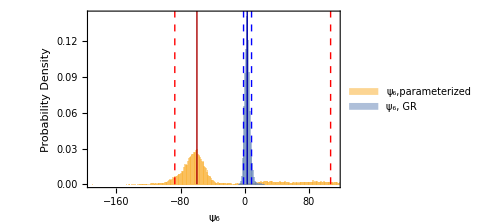

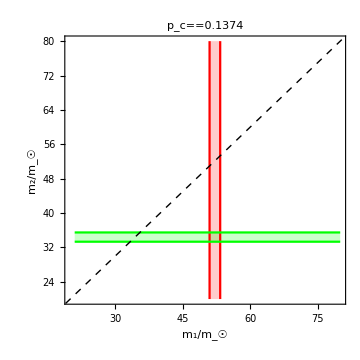

```mathematica
m1s=Range[20,80,1];
m2s=Range[20,80,1];

order=6;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.1374;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

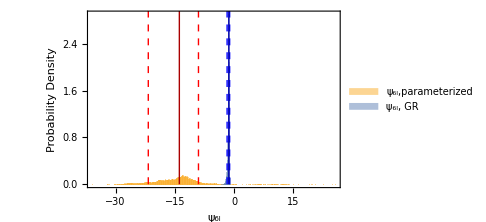

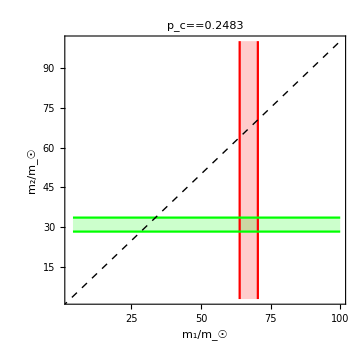

```mathematica
m1s=Range[3,100,1];
m2s=Range[3,100,1];

order="6l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.2483;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

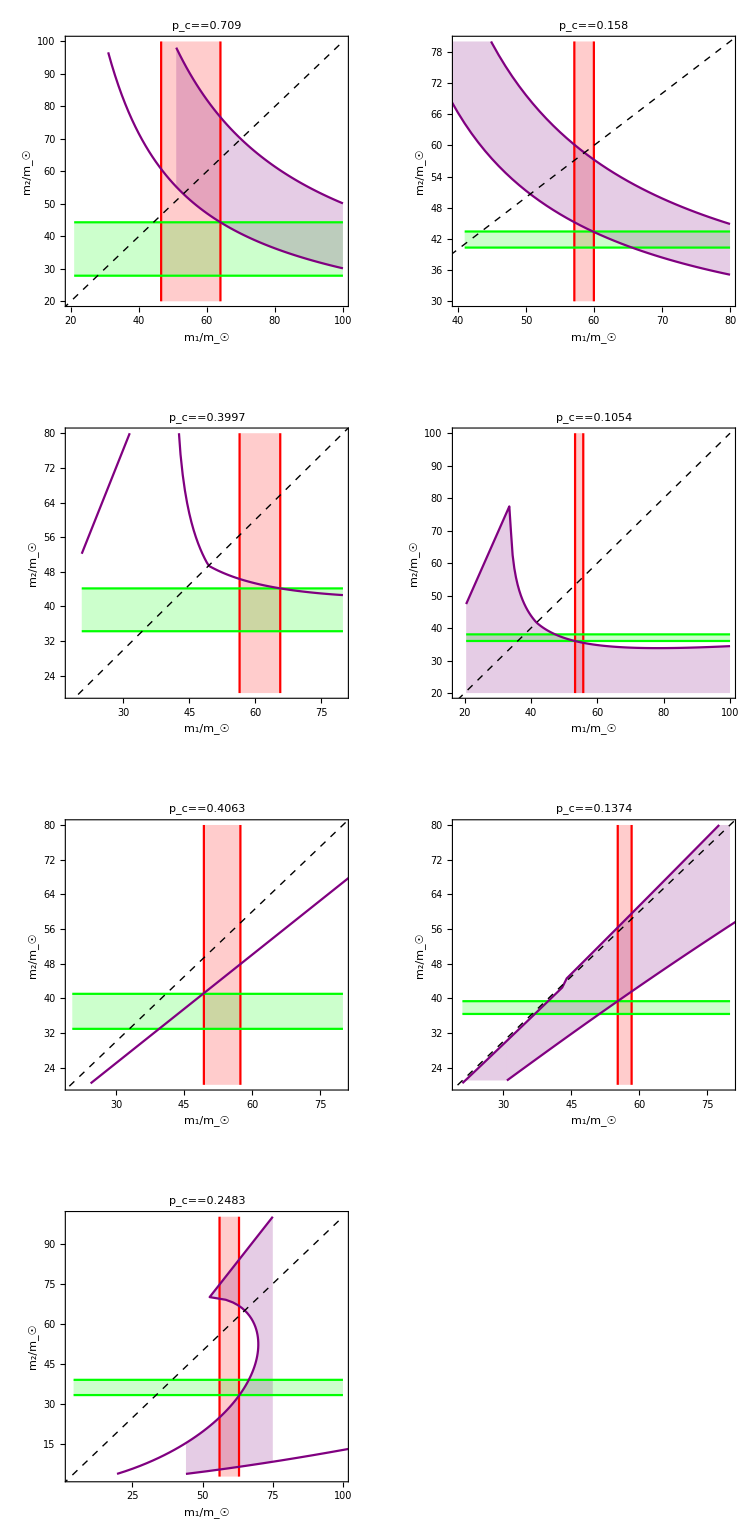

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{plots[[7]],}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

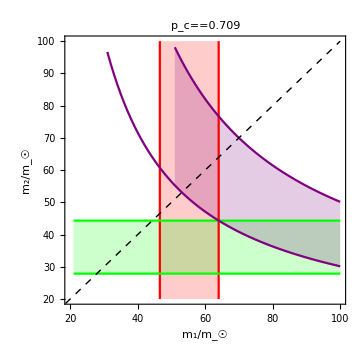
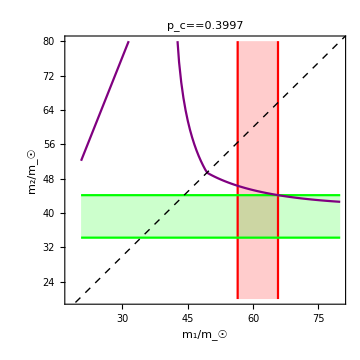
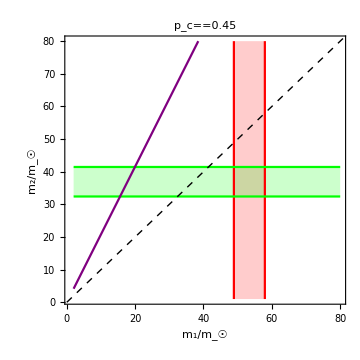
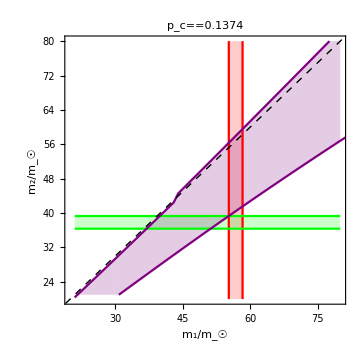

```mathematica
Values[plots[[{1,3,5,6}]]]
```

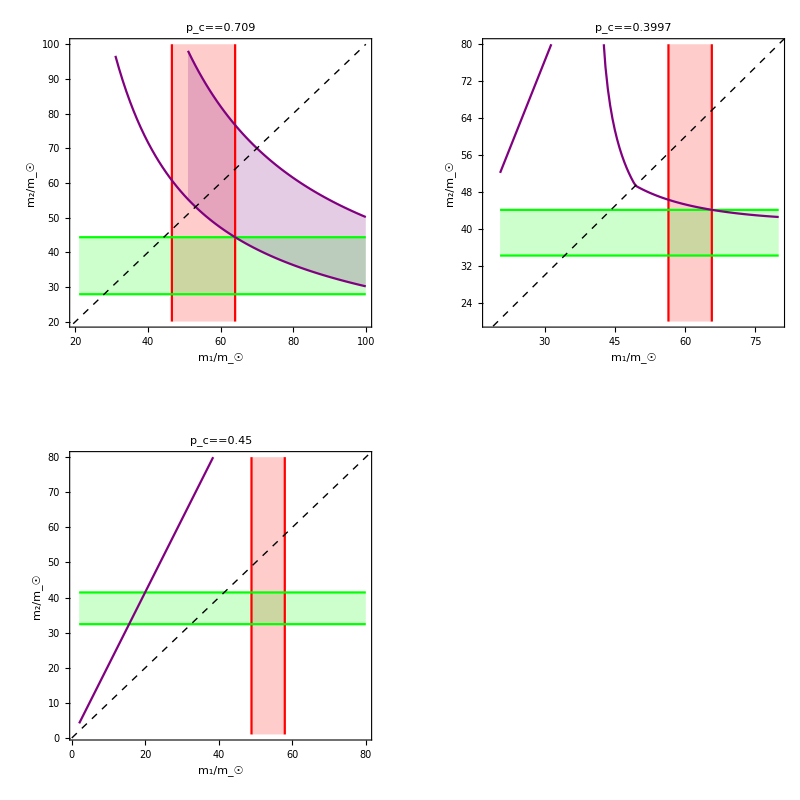

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots[[{1,3}]]],2],{plots[[5]],}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->800,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

```mathematica
Append[Values[plots[[{1,3}]]],{plots[[5]],}]
```

{-Graphics-,-Graphics-,{-Graphics-,Null}}

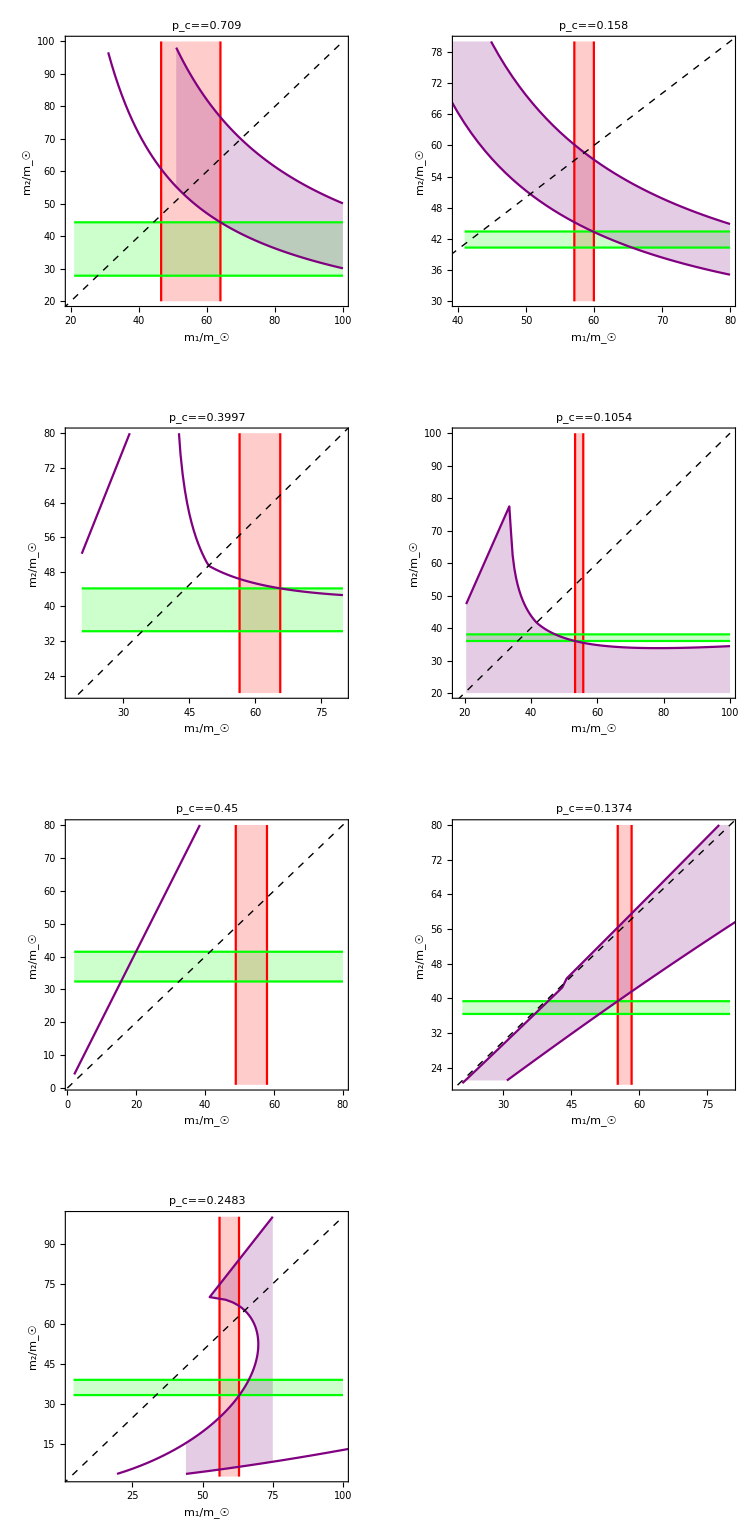

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{plots[[7]],patch6}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

## Value Domains

```mathematica
vd=<||>;
```

```mathematica
(BCI["cpsi0"]["cpsi0"][[3]]-BCI["cpsi0"]["cpsi0"][[1]])/5000
vd["cpsi0"]=Manipulate[
Plot3D[
Function[{m1,m2},Psi[0,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi0"]["mass1"][[1]],BCI["cpsi0"]["mass1"][[3]]},
{m2,BCI["cpsi0"]["mass2"][[1]],BCI["cpsi0"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False,
AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]],TraditionalForm[Subscript[ψ,0]]}
],
{spin1z,BCI["cpsi0"]["spin1z"][[2]]},{spin2z,BCI["cpsi0"]["spin2z"][[2]]}
]
```

0.206569

```mathematica
(BCI["cpsi2"]["cpsi2"][[3]]-BCI["cpsi2"]["cpsi2"][[1]])/250
vd["cpsi0"]=Manipulate[
Plot3D[
Function[{m1,m2},Psi[2,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi2"]["mass1"][[1]],BCI["cpsi2"]["mass1"][[3]]},
{m2,BCI["cpsi2"]["mass2"][[1]],BCI["cpsi2"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi2"]["spin1z"][[2]]},{spin2z,BCI["cpsi2"]["spin2z"][[2]]}
]
```

1.06474

```mathematica
(BCI["cpsi3"]["cpsi3"][[3]]-BCI["cpsi3"]["cpsi3"][[1]])/150
Manipulate[
Plot3D[
Function[{m1,m2},Psi[3,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi3"]["mass1"][[1]],BCI["cpsi3"]["mass1"][[3]]},
{m2,BCI["cpsi3"]["mass2"][[1]],BCI["cpsi3"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi3"]["spin1z"][[2]]},{spin2z,BCI["cpsi3"]["spin2z"][[2]]}
]
```

1.57419

Part::partw: Part 3 of Missing[KeyAbsent,cpsi3][mass1] does not exist.

Plot3D::plln: Limiting value mass1 in {m1,mass1,Missing[KeyAbsent,cpsi3][mass1]⟦3⟧} is not a machine-sized real number.

```mathematica
(BCI["cpsi4"]["cpsi4"][[3]]-BCI["cpsi4"]["cpsi4"][[1]])/5
Manipulate[
Plot3D[
Function[{m1,m2},Psi[4,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi4"]["mass1"][[1]],BCI["cpsi4"]["mass1"][[3]]},
{m2,BCI["cpsi4"]["mass2"][[1]],BCI["cpsi4"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi4"]["spin1z"][[2]]},{spin2z,BCI["cpsi4"]["spin2z"][[2]]}
]
```

23.7613

Part::partw: Part 3 of Missing[KeyAbsent,cpsi4][mass1] does not exist.

Plot3D::plln: Limiting value mass1 in {m1,mass1,Missing[KeyAbsent,cpsi4][mass1]⟦3⟧} is not a machine-sized real number.

```mathematica
(BCI["cpsi5l"]["cpsi5l"][[3]]-BCI["cpsi5l"]["cpsi5l"][[1]])/1.5
Manipulate[
Plot3D[
Function[{m1,m2},Psi["5l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi5l"]["mass1"][[1]],BCI["cpsi5l"]["mass1"][[3]]},
{m2,BCI["cpsi5l"]["mass2"][[1]],BCI["cpsi5l"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi5l"]["spin1z"][[2]]},{spin2z,BCI["cpsi5l"]["spin2z"][[2]]}
]
```

9.56092

Part::partw: Part 3 of Missing[KeyAbsent,cpsi5l][mass1] does not exist.

Plot3D::plln: Limiting value mass1 in {m1,mass1,Missing[KeyAbsent,cpsi5l][mass1]⟦3⟧} is not a machine-sized real number.

```mathematica
Manipulate[
Plot3D[
Function[{m1,m2},Psi["5l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,3,100},
{m2,3,100},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi5l"]["spin1z"][[2]]},{spin2z,BCI["cpsi5l"]["spin2z"][[2]]}
]
```

```mathematica
(BCI["cpsi6"]["cpsi6"][[3]]-BCI["cpsi6"]["cpsi6"][[1]])/0.5
Manipulate[
Plot3D[
Function[{m1,m2},Psi[6,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi6"]["mass1"][[1]],BCI["cpsi6"]["mass1"][[3]]},
{m2,BCI["cpsi6"]["mass2"][[1]],BCI["cpsi6"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi6"]["spin1z"][[2]]},{spin2z,BCI["cpsi6"]["spin2z"][[2]]}
]
```

31.1398

```mathematica
(BCI["cpsi6l"]["cpsi6l"][[3]]-BCI["cpsi6l"]["cpsi6l"][[1]])/0.1
Manipulate[
Plot3D[
Function[{m1,m2},Psi["6l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi6l"]["mass1"][[1]],BCI["cpsi6l"]["mass1"][[3]]},
{m2,BCI["cpsi6l"]["mass2"][[1]],BCI["cpsi6l"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi6l"]["spin1z"][[2]]},{spin2z,BCI["cpsi6l"]["spin2z"][[2]]}
]
```

27.0383

```mathematica
(*Manipulate[
Plot3D[
Function[{m1,m2},Psi[7,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,20,80},
{m2,20,80},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,0.06070798549182338},{spin2z,0.09392835788044217}
(*{spin1z,-1,1},{spin2z,-1,1}*)
]*)
```

## Exports

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/comp_plots/","GW150914_inverse_plot_",
name,
".pdf"];
Export[exportPath,compPlots[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/","GW150914_inverse_plot_",
name,
".pdf"];
Export[exportPath,plots[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

```mathematica
Export["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_patch_cpsi6.pdf",patch6,"PDF",ImageResolution->1000]
```

D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_patch_cpsi6.pdf

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/value_domains/","GW150914_vd_",
name,
".pdf"];
Export[exportPath,vd[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```